```mathematica
Clear["Global`*"]
```

# Substitution

Aim: to check the calculations using the revised method
Logbook_220117

## Misc

```mathematica
CC[x_]:=Cos[σ x] / Cosh[σ x];
SS[x_]:=Sin[σ x] / Sinh[σ x];
LDE[f_]:=D[f[x],{x,4}] + 4 σ^4 f[x] ;
NDE[f_]:=Γ f[x]^3;
```

```mathematica
u[n_]:=x|->Sum[c[i]CC[x]^i SS[x]^((2n+1)-i), {i, 0, 2n+1}]
```

```mathematica
u0[x_]:=A CC[x] + B SS[x];
```

```mathematica
subs = {Tanh[x σ] -> sech/csch, Coth[x σ] -> csch/sech, Sin[xσ] -> sin, Cos[x σ] -> cos, Sech[x σ] -> sech, Csch[x σ] -> csch};
```

```mathematica
(D[CC[x] , {x,4}] // TrigExpand) /. {Tanh[x σ]^2 -> 1 - Sech[x σ]^2, Tanh[x σ]^4 -> (1-Sech[x σ]^2)^2} //Simplify
```

4 σ^4 Sech[x σ] (-Cos[x σ]+6 Cos[x σ] Sech[x σ]^4-2 Sech[x σ]^2 (Cos[x σ]+3 Sin[x σ] Tanh[x σ]))

## New Approach

```mathematica
uu[n_] := (i |-> (x |-> CC[x]^i SS[x]^(2n+1-i)))/@Range[0, 2n+1]
```

```mathematica
uux[x_,n_]:=( f|->f[x])/@uu[n]
```

```mathematica
(
(
(D[#[x], {x,4}] 
)
//. {
Csch[x σ] -> 1/sinh,
Sech[x σ] -> 1/cosh,
Tanh[x σ] -> sinh/cosh,
Coth[x σ] -> cosh/sinh,
Cos[x σ]-> cos,
Sin[x σ]-> sin
}
) 
// FullSimplify
// (u |->Collect[u, {cosh,sinh}])
)&/@
uu[0]
```

{(5 sin σ^4)/sinh^5+(cosh^4 sin σ^4)/sinh^5-(4 cos cosh^3 σ^4)/sinh^4-(6 sin σ^4)/sinh^3+(sin σ^4)/sinh+cosh^2 ((18 sin σ^4)/sinh^5-(6 sin σ^4)/sinh^3)+cosh (-(20 cos σ^4)/sinh^4+(4 cos σ^4)/sinh^2),(cos σ^4)/cosh-(4 sin sinh σ^4)/cosh^2+(6 cos σ^4-6 cos sinh^2 σ^4)/cosh^3+(-20 sin sinh σ^4+4 sin sinh^3 σ^4)/cosh^4+(5 cos σ^4-18 cos sinh^2 σ^4+cos sinh^4 σ^4)/cosh^5}

```mathematica
(
(
(D[#[x], {x,4}] 
)
) 
// (u |->FullSimplify[u, ExcludedForms->{Sech[_]}, ComplexityFunction->(e|-> (100 Count[e,_Coth|_Tanh|_Cot|_Tan, {0, Infinity}] + LeafCount[e]))])
// (u |-> Collect[u, {Cosh[x σ], Sinh[x σ]}])
)&/@
uu[0]
```

{1/4 σ^4 Csch[x σ]^5 (-2 (-37-12 Cosh[2 x σ]+Cosh[4 x σ]) Sin[x σ]-48 Cos[x σ] Sinh[2 x σ]),1/2 σ^4 Csc[x σ] Sech[x σ] (1+6 Sech[x σ]^2+5 Sech[x σ]^4) Sin[2 x σ]-8 σ^4 Csch[2 x σ] (1+5 Sech[x σ]^2) Sin[x σ] Sinh[x σ] Tanh[x σ]-12 σ^4 Csc[x σ] Csch[2 x σ]^2 (1+3 Sech[x σ]^2) Sin[2 x σ] Sinh[x σ]^3 Tanh[x σ]+32 σ^4 Csch[2 x σ]^3 Sin[x σ] Sinh[x σ]^5 Tanh[x σ]+8 σ^4 Csc[x σ] Csch[2 x σ]^4 Sin[2 x σ] Sinh[x σ]^7 Tanh[x σ]}

```mathematica
(
(
(D[#[x], {x,4}] 
//TrigToExp)
) 
// FullSimplify // TrigToExp // Simplify
// (u |->Collect[u, {cosh,sinh}])
)&/@
uu[0]
```

{(4 ⅇ^((1-ⅈ) x σ) (-24 ⅇ^(2 x σ) (1+ⅇ^(2 ⅈ x σ)) (-1+ⅇ^(4 x σ))+ⅈ (-1+ⅇ^(2 ⅈ x σ)) (1-12 ⅇ^(2 x σ)-74 ⅇ^(4 x σ)-12 ⅇ^(6 x σ)+ⅇ^(8 x σ))) σ^4)/((-1+ⅇ^(2 x σ))^5),-(4 ⅇ^((1-ⅈ) x σ) (1+ⅇ^(2 ⅈ x σ)+(12-24 ⅈ) ⅇ^(2 x σ)+(12+24 ⅈ) ⅇ^((2+2 ⅈ) x σ)-74 ⅇ^(4 x σ)-74 ⅇ^((4+2 ⅈ) x σ)+(12+24 ⅈ) ⅇ^(6 x σ)+(12-24 ⅈ) ⅇ^((6+2 ⅈ) x σ)+ⅇ^(8 x σ)+ⅇ^((8+2 ⅈ) x σ)) σ^4)/((1+ⅇ^(2 x σ))^5)}

```mathematica
(((D[#,{x,4}]
//TrigExpand)
//. {
Tanh[x σ] -> Sinh[x σ] Sech[x σ],
Tanh[x σ]^2 -> 1 - Sech[x σ]^2, Tanh[x σ]^4 -> (1-Sech[x σ]^2)^2, Coth[x σ]^2 -> 1 +Csch[x σ]^2, Coth[x σ]^4 -> (1+Csch[x σ]^2)^2
} 
// (u |-> Collect[u, {Csch[x σ], Sech[x σ]}])
)
/. {
Csch[x σ] -> csch,
Sech[x σ] -> sech,
Tanh[x σ] -> sech/csch,
Coth[x σ] -> csch/sech,
Cos[x σ]-> cos,
Sin[x σ]-> sin
}
//Simplify
)&/@
uux[x,1]
```

{1/sech^3 3 csch^3 (60 cos^3 csch^3 sech^2+3 cos^2 (27+20 csch^2-30 csch^4) sech^3 sin+sech^3 sin (7-27 sin^2+csch^2 (84-20 sin^2)+30 csch^4 (3+sin^2))-12 cos csch (sech^2+csch^2 (1+sech^2 (4+15 sin^2)))) σ^4,1/(128 csch sech^3)(-cos^3 csch (sech^6 (-2349+sech^2)+2 csch^2 sech^4 (-2835-600 sech^2+242 sech^4)+4 csch^4 sech^2 (-567-300 sech^2+726 sech^4+404 sech^6)+csch^6 (-81-80 sech^2+484 sech^4+1616 sech^6+1901 sech^8))-288 cos^2 csch^2 sech^3 (15 sech^4+10 csch^2 sech^2 (5+6 sech^2)+3 csch^4 (5+20 sech^2+7 sech^4)) sin+96 sech^3 sin (2 sech^4+csch^2 sech^2 (14+3 sech^2 (2+5 sin^2))+csch^6 (8+15 sin^2+3 sech^4 (2+7 sin^2)+6 sech^2 (3+10 sin^2))+2 csch^4 (8+5 sech^2 (2+5 sin^2)+sech^4 (9+30 sin^2)))+cos (csch sech^6 (203-7047 sin^2+3 sech^2 (35+sin^2))+2 csch^3 sech^4 (245-8505 sin^2-120 sech^2 (-7+15 sin^2)+6 sech^4 (75+121 sin^2))+4 csch^5 sech^2 (49-1701 sin^2-60 sech^2 (-7+15 sin^2)+18 sech^4 (75+121 sin^2)+4 sech^6 (89+303 sin^2))+csch^7 (7-243 sin^2-16 sech^2 (-7+15 sin^2)+12 sech^4 (75+121 sin^2)+16 sech^6 (89+303 sin^2)+sech^8 (1397+5703 sin^2)))) σ^4,1/(128 csch^3 sech)(96 cos^3 (15 csch^3 sech^6+3 csch^7 sech^2 (5-20 sech^2+7 sech^4)+csch^5 (50 sech^4-60 sech^6))+3 cos^2 sech (-81 sech^6+4 csch^2 sech^4 (-567+20 sech^2)+2 csch^4 sech^2 (-2835+600 sech^2+242 sech^4)+csch^6 (-2349+1200 sech^2+2904 sech^4-1616 sech^6)+csch^8 (-1+484 sech^2-1616 sech^4+1901 sech^6)) sin-96 cos (csch^3 sech^4 (16+sech^2 (-8+45 sin^2))+csch^7 (2+sech^4 (18-180 sin^2)+sech^2 (-6+45 sin^2)+sech^6 (-6+63 sin^2))-2 csch^5 sech^2 (-7+sech^2 (10-75 sin^2)+sech^4 (-9+90 sin^2)))+sech sin (sech^6 (7+81 sin^2)-4 csch^2 sech^4 (4 sech^2 (7+5 sin^2)-7 (7+81 sin^2))+csch^8 (-105+sin^2+sech^6 (1397-1901 sin^2)+sech^2 (900-484 sin^2)+16 sech^4 (-89+101 sin^2))+csch^6 (sech^4 (5400-2904 sin^2)-240 sech^2 (7+5 sin^2)+29 (7+81 sin^2)+16 sech^6 (-89+101 sin^2))-2 csch^4 sech^2 (120 sech^2 (7+5 sin^2)-35 (7+81 sin^2)+sech^4 (-450+242 sin^2)))) σ^4,1/csch^3 3 sech^3 (cos^3 csch^3 (-27+20 sech^2+30 sech^4)-180 cos^2 csch^2 sech^3 sin+cos csch^3 (7+81 sin^2-90 sech^4 (-1+sin^2)-12 sech^2 (7+5 sin^2))+12 sech sin (sech^2+csch^2 (1+sech^2 (-4+5 sin^2)))) σ^4}

```mathematica
(f |->((D[f[x],{x,4}] // TrigExpand) /. {Tanh[x σ]^2 -> 1 - Sech[x σ]^2, Tanh[x σ]^4 -> (1-Sech[x σ]^2)^2} //Simplify))/@uu[0] // MatrixForm
```

(1/4 σ^4 Csch[x σ]^5 (74 Sin[x σ]+(12+24 ⅈ) Sin[(1+2 ⅈ) x σ]-Sin[(1+4 ⅈ) x σ]-(24+12 ⅈ) Sinh[(2+ⅈ) x σ]+ⅈ Sinh[(4+ⅈ) x σ])
4 σ^4 Sech[x σ] (-Cos[x σ]+6 Cos[x σ] Sech[x σ]^4-2 Sech[x σ]^2 (Cos[x σ]+3 Sin[x σ] Tanh[x σ])))

## Just do it manually

```mathematica
Simplification = {Tanh[σ x] -> 1, Coth[σ x] -> 1, Csch[σ x] ->Sech[σ x], Cos[σ x] -> 1, Sin[σ x] -> 1};
```

Give up trying to make a nice script, just work through it with Mathematica as an aid.

1. Check if u0 satisfies the linear ODE up to the first order

```mathematica
Collect[LDE[u[0]] /. Simplification, {Sech[x σ]}]
```

(-8 σ^4 c[0]-32 σ^4 c[1]) Sech[x σ]^3+(5 σ^4 c[0]+5 σ^4 c[1]) Sech[x σ]^5

Yes it does

2. Then we need to define the u1 function by letting this == 0 (up to third order)

```mathematica
Collect[(LDE[u[1]] + NDE[x |-> A CC[x] + B CC[x]]) /. Simplification, Sech[x σ]]
```

(A^3 Γ+3 A^2 B Γ+3 A B^2 Γ+B^3 Γ+64 σ^4 c[0]-96 σ^4 c[1]-192 σ^4 c[2]+352 σ^4 c[3]) Sech[x σ]^3+(-96 σ^4 c[0]+8 σ^4 c[1]-96 σ^4 c[2]-696 σ^4 c[3]) Sech[x σ]^5+(33 σ^4 c[0]+9 σ^4 c[1]+9 σ^4 c[2]+33 σ^4 c[3]) Sech[x σ]^7

Based on the limit --> infinity, it may be possible for there to be a c[1] etc so that the sech^3 term is 0. Need to probe deeper to find out what that may be:

```mathematica
unwieldy = LDE[u[1]] + NDE[x |-> A CC[x] + B SS[x]]
```

12 σ c[0] Cos[x σ] (-27 σ^3 Coth[x σ]^3 Csch[x σ]^3-33 σ^3 Coth[x σ] Csch[x σ]^5) Sin[x σ]^2+c[0] (81 σ^4 Coth[x σ]^4 Csch[x σ]^3+246 σ^4 Coth[x σ]^2 Csch[x σ]^5+33 σ^4 Csch[x σ]^7) Sin[x σ]^3+Γ (A Cos[x σ] Sech[x σ]+B Csch[x σ] Sin[x σ])^3+Sech[x σ] Sin[x σ]^2 (σ^4 c[1] Cos[x σ] Csch[x σ]^2-6 σ^2 c[1] Cos[x σ] (4 σ^2 Coth[x σ]^2 Csch[x σ]^2+2 σ^2 Csch[x σ]^4)+c[1] Cos[x σ] (16 σ^4 Coth[x σ]^4 Csch[x σ]^2+88 σ^4 Coth[x σ]^2 Csch[x σ]^4+16 σ^4 Csch[x σ]^6)-8 σ^4 c[1] Coth[x σ] Csch[x σ]^2 Sin[x σ]-4 σ c[1] (-8 σ^3 Coth[x σ]^3 Csch[x σ]^2-16 σ^3 Coth[x σ] Csch[x σ]^4) Sin[x σ])-12 σ c[0] Coth[x σ] Csch[x σ]^3 (6 σ^3 Cos[x σ]^3-21 σ^3 Cos[x σ] Sin[x σ]^2)+c[3] Sech[x σ]^3 (21 σ^4 Cos[x σ]^3-60 σ^4 Cos[x σ] Sin[x σ]^2)+6 c[0] (9 σ^2 Coth[x σ]^2 Csch[x σ]^3+3 σ^2 Csch[x σ]^5) (6 σ^2 Cos[x σ]^2 Sin[x σ]-3 σ^2 Sin[x σ]^3)+c[0] Csch[x σ]^3 (-60 σ^4 Cos[x σ]^2 Sin[x σ]+21 σ^4 Sin[x σ]^3)+4 σ^4 (c[3] Cos[x σ]^3 Sech[x σ]^3+c[2] Cos[x σ]^2 Csch[x σ] Sech[x σ]^2 Sin[x σ]+c[1] Cos[x σ] Csch[x σ]^2 Sech[x σ] Sin[x σ]^2+c[0] Csch[x σ]^3 Sin[x σ]^3)+Sech[x σ]^2 Sin[x σ] (c[2] Cos[x σ]^2 (σ^4 Coth[x σ]^4 Csch[x σ]+18 σ^4 Coth[x σ]^2 Csch[x σ]^3+5 σ^4 Csch[x σ]^5)-32 σ^4 c[2] Cos[x σ] Coth[x σ] Csch[x σ] Sin[x σ]-8 σ c[2] Cos[x σ] (-σ^3 Coth[x σ]^3 Csch[x σ]-5 σ^3 Coth[x σ] Csch[x σ]^3) Sin[x σ]+6 c[2] (σ^2 Coth[x σ]^2 Csch[x σ]+σ^2 Csch[x σ]^3) (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)+c[2] Csch[x σ] (8 σ^4 Cos[x σ]^2-8 σ^4 Sin[x σ]^2))-12 σ c[3] Sech[x σ]^3 (21 σ^3 Cos[x σ]^2 Sin[x σ]-6 σ^3 Sin[x σ]^3) Tanh[x σ]+4 (c[2] Cos[x σ]^2 (-σ^3 Coth[x σ]^3 Csch[x σ]-5 σ^3 Coth[x σ] Csch[x σ]^3)+8 σ^3 c[2] Cos[x σ] Csch[x σ] Sin[x σ]-6 σ c[2] Cos[x σ] (σ^2 Coth[x σ]^2 Csch[x σ]+σ^2 Csch[x σ]^3) Sin[x σ]-3 σ c[2] Coth[x σ] Csch[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)) (σ Cos[x σ] Sech[x σ]^2-2 σ Sech[x σ]^2 Sin[x σ] Tanh[x σ])+4 (6 σ^3 c[1] Cos[x σ] Coth[x σ] Csch[x σ]^2+c[1] Cos[x σ] (-8 σ^3 Coth[x σ]^3 Csch[x σ]^2-16 σ^3 Coth[x σ] Csch[x σ]^4)+σ^3 c[1] Csch[x σ]^2 Sin[x σ]-3 σ c[1] (4 σ^2 Coth[x σ]^2 Csch[x σ]^2+2 σ^2 Csch[x σ]^4) Sin[x σ]) (2 σ Cos[x σ] Sech[x σ] Sin[x σ]-σ Sech[x σ] Sin[x σ]^2 Tanh[x σ])+6 c[3] (-3 σ^2 Cos[x σ]^3+6 σ^2 Cos[x σ] Sin[x σ]^2) (-3 σ^2 Sech[x σ]^5+9 σ^2 Sech[x σ]^3 Tanh[x σ]^2)-12 σ c[3] Cos[x σ]^2 Sin[x σ] (33 σ^3 Sech[x σ]^5 Tanh[x σ]-27 σ^3 Sech[x σ]^3 Tanh[x σ]^3)+c[3] Cos[x σ]^3 (33 σ^4 Sech[x σ]^7-246 σ^4 Sech[x σ]^5 Tanh[x σ]^2+81 σ^4 Sech[x σ]^3 Tanh[x σ]^4)+6 (-σ^2 c[1] Cos[x σ] Csch[x σ]^2+c[1] Cos[x σ] (4 σ^2 Coth[x σ]^2 Csch[x σ]^2+2 σ^2 Csch[x σ]^4)+4 σ^2 c[1] Coth[x σ] Csch[x σ]^2 Sin[x σ]) (Sech[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)-4 σ^2 Cos[x σ] Sech[x σ] Sin[x σ] Tanh[x σ]+Sin[x σ]^2 (-σ^2 Sech[x σ]^3+σ^2 Sech[x σ] Tanh[x σ]^2))+6 (c[2] Cos[x σ]^2 (σ^2 Coth[x σ]^2 Csch[x σ]+σ^2 Csch[x σ]^3)+4 σ^2 c[2] Cos[x σ] Coth[x σ] Csch[x σ] Sin[x σ]+c[2] Csch[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)) (-σ^2 Sech[x σ]^2 Sin[x σ]-4 σ^2 Cos[x σ] Sech[x σ]^2 Tanh[x σ]+Sin[x σ] (-2 σ^2 Sech[x σ]^4+4 σ^2 Sech[x σ]^2 Tanh[x σ]^2))+4 (-2 σ c[1] Cos[x σ] Coth[x σ] Csch[x σ]^2-σ c[1] Csch[x σ]^2 Sin[x σ]) (-8 σ^3 Cos[x σ] Sech[x σ] Sin[x σ]-3 σ Sech[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2) Tanh[x σ]+6 σ Cos[x σ] Sin[x σ] (-σ^2 Sech[x σ]^3+σ^2 Sech[x σ] Tanh[x σ]^2)+Sin[x σ]^2 (5 σ^3 Sech[x σ]^3 Tanh[x σ]-σ^3 Sech[x σ] Tanh[x σ]^3))+4 (-σ c[2] Cos[x σ]^2 Coth[x σ] Csch[x σ]-2 σ c[2] Cos[x σ] Csch[x σ] Sin[x σ]) (-σ^3 Cos[x σ] Sech[x σ]^2+6 σ^3 Sech[x σ]^2 Sin[x σ] Tanh[x σ]+3 σ Cos[x σ] (-2 σ^2 Sech[x σ]^4+4 σ^2 Sech[x σ]^2 Tanh[x σ]^2)+Sin[x σ] (16 σ^3 Sech[x σ]^4 Tanh[x σ]-8 σ^3 Sech[x σ]^2 Tanh[x σ]^3))+c[1] Cos[x σ] Csch[x σ]^2 (Sech[x σ] (-8 σ^4 Cos[x σ]^2+8 σ^4 Sin[x σ]^2)+32 σ^4 Cos[x σ] Sech[x σ] Sin[x σ] Tanh[x σ]+6 (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2) (-σ^2 Sech[x σ]^3+σ^2 Sech[x σ] Tanh[x σ]^2)+8 σ Cos[x σ] Sin[x σ] (5 σ^3 Sech[x σ]^3 Tanh[x σ]-σ^3 Sech[x σ] Tanh[x σ]^3)+Sin[x σ]^2 (5 σ^4 Sech[x σ]^5-18 σ^4 Sech[x σ]^3 Tanh[x σ]^2+σ^4 Sech[x σ] Tanh[x σ]^4))+c[2] Cos[x σ]^2 Csch[x σ] (σ^4 Sech[x σ]^2 Sin[x σ]+8 σ^4 Cos[x σ] Sech[x σ]^2 Tanh[x σ]-6 σ^2 Sin[x σ] (-2 σ^2 Sech[x σ]^4+4 σ^2 Sech[x σ]^2 Tanh[x σ]^2)+4 σ Cos[x σ] (16 σ^3 Sech[x σ]^4 Tanh[x σ]-8 σ^3 Sech[x σ]^2 Tanh[x σ]^3)+Sin[x σ] (16 σ^4 Sech[x σ]^6-88 σ^4 Sech[x σ]^4 Tanh[x σ]^2+16 σ^4 Sech[x σ]^2 Tanh[x σ]^4))

This is very unwieldy to work with

#### Grouping

Instead, group it by coefficients of sech and csch, and then only consider the ones that combine to create order 3 or less 
	Note: Need to make sure that there aren’t cosh or sinh terms mixing up the orders 
	Also for some reason not all of the sech and csch terms are filtered out so need to do sech twice

```mathematica
MatrixForm/@(eqns = CoefficientList[CoefficientList[CoefficientList[unwieldy, Sech[x σ]], Csch[x σ]], Sech[x σ]] /. {A -> 0.4384, B -> 1.0170, Γ -> 24, σ -> 6^(1/4)} // N )
```

{({}
{}
{}
{-1944. c[0.] Cos[1.56508 x] Coth[1.56508 x]^3 Sin[1.56508 x]^2+24. c[0.] Sin[1.56508 x]^3+486. c[0.] Coth[1.56508 x]^4 Sin[1.56508 x]^3-18.781 c[0.] Coth[1.56508 x] (23.002 Cos[1.56508 x]^3-80.5068 Cos[1.56508 x] Sin[1.56508 x]^2)+132.272 c[0.] Coth[1.56508 x]^2 (14.6969 Cos[1.56508 x]^2 Sin[1.56508 x]-7.34847 Sin[1.56508 x]^3)+c[0.] (-360. Cos[1.56508 x]^2 Sin[1.56508 x]+126. Sin[1.56508 x]^3)}
{}
{-2376. c[0.] Cos[1.56508 x] Coth[1.56508 x] Sin[1.56508 x]^2+1476. c[0.] Coth[1.56508 x]^2 Sin[1.56508 x]^3+44.0908 c[0.] (14.6969 Cos[1.56508 x]^2 Sin[1.56508 x]-7.34847 Sin[1.56508 x]^3)}
{}
{198. c[0.] Sin[1.56508 x]^3}),({0.,0.,-132. c[1.] Cos[1.56508 x] Sin[1.56508 x]^2+24. c[1.] Sin[1.56508 x]^3 Tanh[1.56508 x]}
{0.,-144. c[1.] Cos[1.56508 x]^2 Sin[1.56508 x]+120. c[1.] Sin[1.56508 x]^3+29.3939 c[1.] Sin[1.56508 x] (4.89898 Cos[1.56508 x]^2-4.89898 Sin[1.56508 x]^2)}
{96. c[1.] Cos[1.56508 x]^2 Coth[1.56508 x] Sin[1.56508 x]-384. c[1.] Cos[1.56508 x]^2 Coth[1.56508 x]^3 Sin[1.56508 x]-306. c[1.] Cos[1.56508 x] Sin[1.56508 x]^2-528. c[1.] Cos[1.56508 x] Coth[1.56508 x]^2 Sin[1.56508 x]^2+96. c[1.] Cos[1.56508 x] Coth[1.56508 x]^4 Sin[1.56508 x]^2+240. c[1.] Coth[1.56508 x] Sin[1.56508 x]^3+192. c[1.] Coth[1.56508 x]^3 Sin[1.56508 x]^3+44.0908 c[1.] Cos[1.56508 x] (4.89898 Cos[1.56508 x]^2-4.89898 Sin[1.56508 x]^2)+58.7878 c[1.] Cos[1.56508 x] Coth[1.56508 x]^2 (4.89898 Cos[1.56508 x]^2-4.89898 Sin[1.56508 x]^2)+58.7878 c[1.] Coth[1.56508 x] Sin[1.56508 x] (4.89898 Cos[1.56508 x]^2-4.89898 Sin[1.56508 x]^2)+c[1.] Cos[1.56508 x] (-48. Cos[1.56508 x]^2+48. Sin[1.56508 x]^2),0.,72. c[1.] Cos[1.56508 x] Sin[1.56508 x]^2}
{0.,-288. c[1.] Cos[1.56508 x]^2 Sin[1.56508 x]+144. c[1.] Sin[1.56508 x]^3}
{-768. c[1.] Cos[1.56508 x]^2 Coth[1.56508 x] Sin[1.56508 x]+24. c[1.] Cos[1.56508 x] Sin[1.56508 x]^2+528. c[1.] Cos[1.56508 x] Coth[1.56508 x]^2 Sin[1.56508 x]^2+384. c[1.] Coth[1.56508 x] Sin[1.56508 x]^3+29.3939 c[1.] Cos[1.56508 x] (4.89898 Cos[1.56508 x]^2-4.89898 Sin[1.56508 x]^2)}
{}
{96. c[1.] Cos[1.56508 x] Sin[1.56508 x]^2}),({0.,-288. c[2.] Cos[1.56508 x]^3-96. c[2.] Cos[1.56508 x] Sin[1.56508 x]^2-58.7878 c[2.] Cos[1.56508 x] (-4.89898 Cos[1.56508 x]^2+4.89898 Sin[1.56508 x]^2)-384. c[2.] Cos[1.56508 x]^2 Sin[1.56508 x] Tanh[1.56508 x]+58.7878 c[2.] Sin[1.56508 x] (-4.89898 Cos[1.56508 x]^2+4.89898 Sin[1.56508 x]^2) Tanh[1.56508 x]+384. c[2.] Cos[1.56508 x] Sin[1.56508 x]^2 Tanh[1.56508 x]^2}
{-120. c[2.] Cos[1.56508 x]^3 Coth[1.56508 x]-24. c[2.] Cos[1.56508 x]^3 Coth[1.56508 x]^3+192. c[1.] Cos[1.56508 x]^2 Sin[1.56508 x]-306. c[2.] Cos[1.56508 x]^2 Sin[1.56508 x]-132. c[2.] Cos[1.56508 x]^2 Coth[1.56508 x]^2 Sin[1.56508 x]+6. c[2.] Cos[1.56508 x]^2 Coth[1.56508 x]^4 Sin[1.56508 x]-48. c[2.] Cos[1.56508 x] Coth[1.56508 x] Sin[1.56508 x]^2+48. c[2.] Cos[1.56508 x] Coth[1.56508 x]^3 Sin[1.56508 x]^2+c[2.] Sin[1.56508 x] (48. Cos[1.56508 x]^2-48. Sin[1.56508 x]^2)-29.3939 c[2.] Cos[1.56508 x] Coth[1.56508 x] (-4.89898 Cos[1.56508 x]^2+4.89898 Sin[1.56508 x]^2)+44.0908 c[2.] Sin[1.56508 x] (-4.89898 Cos[1.56508 x]^2+4.89898 Sin[1.56508 x]^2)+14.6969 c[2.] Coth[1.56508 x]^2 Sin[1.56508 x] (-4.89898 Cos[1.56508 x]^2+4.89898 Sin[1.56508 x]^2),0.,144. c[2.] Cos[1.56508 x]^2 Sin[1.56508 x]}
{0.,-144. c[2.] Cos[1.56508 x]^3+288. c[2.] Cos[1.56508 x] Sin[1.56508 x]^2}
{-120. c[2.] Cos[1.56508 x]^3 Coth[1.56508 x]+60. c[2.] Cos[1.56508 x]^2 Sin[1.56508 x]+108. c[2.] Cos[1.56508 x]^2 Coth[1.56508 x]^2 Sin[1.56508 x]+240. c[2.] Cos[1.56508 x] Coth[1.56508 x] Sin[1.56508 x]^2+14.6969 c[2.] Sin[1.56508 x] (-4.89898 Cos[1.56508 x]^2+4.89898 Sin[1.56508 x]^2)}
{}
{30. c[2.] Cos[1.56508 x]^2 Sin[1.56508 x]}),({73.9875 Cos[1.56508 x]^3+48. c[2.] Cos[1.56508 x]^3+24. c[3.] Cos[1.56508 x]^3+14.6969 c[1.] Cos[1.56508 x] (4.89898 Cos[1.56508 x]^2-4.89898 Sin[1.56508 x]^2)+c[3.] (126. Cos[1.56508 x]^3-360. Cos[1.56508 x] Sin[1.56508 x]^2)-48. c[1.] Cos[1.56508 x]^2 Sin[1.56508 x] Tanh[1.56508 x]-144. c[2.] Cos[1.56508 x]^2 Sin[1.56508 x] Tanh[1.56508 x]-18.781 c[3.] (80.5068 Cos[1.56508 x]^2 Sin[1.56508 x]-23.002 Sin[1.56508 x]^3) Tanh[1.56508 x]-192. c[2.] Cos[1.56508 x]^3 Tanh[1.56508 x]^2+6. c[1.] Cos[1.56508 x] Sin[1.56508 x]^2 Tanh[1.56508 x]^2+132.272 c[3.] (-7.34847 Cos[1.56508 x]^3+14.6969 Cos[1.56508 x] Sin[1.56508 x]^2) Tanh[1.56508 x]^2+96. c[2.] Cos[1.56508 x]^2 Sin[1.56508 x] Tanh[1.56508 x]^3+1944. c[3.] Cos[1.56508 x]^2 Sin[1.56508 x] Tanh[1.56508 x]^3+486. c[3.] Cos[1.56508 x]^3 Tanh[1.56508 x]^4}
{0.,-120. c[1.] Sin[1.56508 x]^3}
{288. c[1.] Cos[1.56508 x]^2 Coth[1.56508 x] Sin[1.56508 x]-60. c[1.] Cos[1.56508 x] Sin[1.56508 x]^2-144. c[1.] Cos[1.56508 x] Coth[1.56508 x]^2 Sin[1.56508 x]^2-144. c[1.] Coth[1.56508 x] Sin[1.56508 x]^3-14.6969 c[1.] Cos[1.56508 x] (4.89898 Cos[1.56508 x]^2-4.89898 Sin[1.56508 x]^2)}
{}
{-72. c[1.] Cos[1.56508 x] Sin[1.56508 x]^2}),({0.,-768. c[2.] Cos[1.56508 x] Sin[1.56508 x]^2}
{144. c[2.] Cos[1.56508 x]^3 Coth[1.56508 x]+240. c[1.] Cos[1.56508 x]^2 Sin[1.56508 x]-24. c[2.] Cos[1.56508 x]^2 Sin[1.56508 x]-72. c[2.] Cos[1.56508 x]^2 Coth[1.56508 x]^2 Sin[1.56508 x]-288. c[2.] Cos[1.56508 x] Coth[1.56508 x] Sin[1.56508 x]^2-29.3939 c[2.] Sin[1.56508 x] (-4.89898 Cos[1.56508 x]^2+4.89898 Sin[1.56508 x]^2)}
{}
{-72. c[2.] Cos[1.56508 x]^2 Sin[1.56508 x]}),({384. c[2.] Cos[1.56508 x]^3-108. c[1.] Cos[1.56508 x] Sin[1.56508 x]^2-44.0908 c[3.] (-7.34847 Cos[1.56508 x]^3+14.6969 Cos[1.56508 x] Sin[1.56508 x]^2)-528. c[2.] Cos[1.56508 x]^2 Sin[1.56508 x] Tanh[1.56508 x]-2376. c[3.] Cos[1.56508 x]^2 Sin[1.56508 x] Tanh[1.56508 x]-1476. c[3.] Cos[1.56508 x]^3 Tanh[1.56508 x]^2}
{}
{30. c[1.] Cos[1.56508 x] Sin[1.56508 x]^2}),({}
{96. c[2.] Cos[1.56508 x]^2 Sin[1.56508 x]}),(198. c[3.] Cos[1.56508 x]^3)}

```mathematica
MatrixForm/@(eqns = CoefficientList[CoefficientList[CoefficientList[unwieldy, Sech[x σ]], Csch[x σ]], Sech[x σ]] )
```

{({}
{}
{}
{-324 σ^4 c[0] Cos[x σ] Coth[x σ]^3 Sin[x σ]^2+B^3 Γ Sin[x σ]^3+4 σ^4 c[0] Sin[x σ]^3+81 σ^4 c[0] Coth[x σ]^4 Sin[x σ]^3-12 σ c[0] Coth[x σ] (6 σ^3 Cos[x σ]^3-21 σ^3 Cos[x σ] Sin[x σ]^2)+54 σ^2 c[0] Coth[x σ]^2 (6 σ^2 Cos[x σ]^2 Sin[x σ]-3 σ^2 Sin[x σ]^3)+c[0] (-60 σ^4 Cos[x σ]^2 Sin[x σ]+21 σ^4 Sin[x σ]^3)}
{}
{-396 σ^4 c[0] Cos[x σ] Coth[x σ] Sin[x σ]^2+246 σ^4 c[0] Coth[x σ]^2 Sin[x σ]^3+18 σ^2 c[0] (6 σ^2 Cos[x σ]^2 Sin[x σ]-3 σ^2 Sin[x σ]^3)}
{}
{33 σ^4 c[0] Sin[x σ]^3}),({0,0,-22 σ^4 c[1] Cos[x σ] Sin[x σ]^2+4 σ^4 c[1] Sin[x σ]^3 Tanh[x σ]}
{0,-24 σ^4 c[1] Cos[x σ]^2 Sin[x σ]+20 σ^4 c[1] Sin[x σ]^3+12 σ^2 c[1] Sin[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)}
{16 σ^4 c[1] Cos[x σ]^2 Coth[x σ] Sin[x σ]-64 σ^4 c[1] Cos[x σ]^2 Coth[x σ]^3 Sin[x σ]+3 A B^2 Γ Cos[x σ] Sin[x σ]^2-51 σ^4 c[1] Cos[x σ] Sin[x σ]^2-88 σ^4 c[1] Cos[x σ] Coth[x σ]^2 Sin[x σ]^2+16 σ^4 c[1] Cos[x σ] Coth[x σ]^4 Sin[x σ]^2+40 σ^4 c[1] Coth[x σ] Sin[x σ]^3+32 σ^4 c[1] Coth[x σ]^3 Sin[x σ]^3+18 σ^2 c[1] Cos[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)+24 σ^2 c[1] Cos[x σ] Coth[x σ]^2 (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)+24 σ^2 c[1] Coth[x σ] Sin[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)+c[1] Cos[x σ] (-8 σ^4 Cos[x σ]^2+8 σ^4 Sin[x σ]^2),0,12 σ^4 c[1] Cos[x σ] Sin[x σ]^2}
{0,-48 σ^4 c[1] Cos[x σ]^2 Sin[x σ]+24 σ^4 c[1] Sin[x σ]^3}
{-128 σ^4 c[1] Cos[x σ]^2 Coth[x σ] Sin[x σ]+4 σ^4 c[1] Cos[x σ] Sin[x σ]^2+88 σ^4 c[1] Cos[x σ] Coth[x σ]^2 Sin[x σ]^2+64 σ^4 c[1] Coth[x σ] Sin[x σ]^3+12 σ^2 c[1] Cos[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)}
{}
{16 σ^4 c[1] Cos[x σ] Sin[x σ]^2}),({0,-48 σ^4 c[2] Cos[x σ]^3-16 σ^4 c[2] Cos[x σ] Sin[x σ]^2-24 σ^2 c[2] Cos[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)-64 σ^4 c[2] Cos[x σ]^2 Sin[x σ] Tanh[x σ]+24 σ^2 c[2] Sin[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2) Tanh[x σ]+64 σ^4 c[2] Cos[x σ] Sin[x σ]^2 Tanh[x σ]^2}
{-20 σ^4 c[2] Cos[x σ]^3 Coth[x σ]-4 σ^4 c[2] Cos[x σ]^3 Coth[x σ]^3+3 A^2 B Γ Cos[x σ]^2 Sin[x σ]+32 σ^4 c[1] Cos[x σ]^2 Sin[x σ]-51 σ^4 c[2] Cos[x σ]^2 Sin[x σ]-22 σ^4 c[2] Cos[x σ]^2 Coth[x σ]^2 Sin[x σ]+σ^4 c[2] Cos[x σ]^2 Coth[x σ]^4 Sin[x σ]-8 σ^4 c[2] Cos[x σ] Coth[x σ] Sin[x σ]^2+8 σ^4 c[2] Cos[x σ] Coth[x σ]^3 Sin[x σ]^2-12 σ^2 c[2] Cos[x σ] Coth[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)+18 σ^2 c[2] Sin[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)+6 σ^2 c[2] Coth[x σ]^2 Sin[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)+c[2] Sin[x σ] (8 σ^4 Cos[x σ]^2-8 σ^4 Sin[x σ]^2),0,24 σ^4 c[2] Cos[x σ]^2 Sin[x σ]}
{0,-24 σ^4 c[2] Cos[x σ]^3+48 σ^4 c[2] Cos[x σ] Sin[x σ]^2}
{-20 σ^4 c[2] Cos[x σ]^3 Coth[x σ]+10 σ^4 c[2] Cos[x σ]^2 Sin[x σ]+18 σ^4 c[2] Cos[x σ]^2 Coth[x σ]^2 Sin[x σ]+40 σ^4 c[2] Cos[x σ] Coth[x σ] Sin[x σ]^2+6 σ^2 c[2] Sin[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)}
{}
{5 σ^4 c[2] Cos[x σ]^2 Sin[x σ]}),({A^3 Γ Cos[x σ]^3+8 σ^4 c[2] Cos[x σ]^3+4 σ^4 c[3] Cos[x σ]^3+6 σ^2 c[1] Cos[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)+c[3] (21 σ^4 Cos[x σ]^3-60 σ^4 Cos[x σ] Sin[x σ]^2)-8 σ^4 c[1] Cos[x σ]^2 Sin[x σ] Tanh[x σ]-24 σ^4 c[2] Cos[x σ]^2 Sin[x σ] Tanh[x σ]-12 σ c[3] (21 σ^3 Cos[x σ]^2 Sin[x σ]-6 σ^3 Sin[x σ]^3) Tanh[x σ]-32 σ^4 c[2] Cos[x σ]^3 Tanh[x σ]^2+σ^4 c[1] Cos[x σ] Sin[x σ]^2 Tanh[x σ]^2+54 σ^2 c[3] (-3 σ^2 Cos[x σ]^3+6 σ^2 Cos[x σ] Sin[x σ]^2) Tanh[x σ]^2+16 σ^4 c[2] Cos[x σ]^2 Sin[x σ] Tanh[x σ]^3+324 σ^4 c[3] Cos[x σ]^2 Sin[x σ] Tanh[x σ]^3+81 σ^4 c[3] Cos[x σ]^3 Tanh[x σ]^4}
{0,-20 σ^4 c[1] Sin[x σ]^3}
{48 σ^4 c[1] Cos[x σ]^2 Coth[x σ] Sin[x σ]-10 σ^4 c[1] Cos[x σ] Sin[x σ]^2-24 σ^4 c[1] Cos[x σ] Coth[x σ]^2 Sin[x σ]^2-24 σ^4 c[1] Coth[x σ] Sin[x σ]^3-6 σ^2 c[1] Cos[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)}
{}
{-12 σ^4 c[1] Cos[x σ] Sin[x σ]^2}),({0,-128 σ^4 c[2] Cos[x σ] Sin[x σ]^2}
{24 σ^4 c[2] Cos[x σ]^3 Coth[x σ]+40 σ^4 c[1] Cos[x σ]^2 Sin[x σ]-4 σ^4 c[2] Cos[x σ]^2 Sin[x σ]-12 σ^4 c[2] Cos[x σ]^2 Coth[x σ]^2 Sin[x σ]-48 σ^4 c[2] Cos[x σ] Coth[x σ] Sin[x σ]^2-12 σ^2 c[2] Sin[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)}
{}
{-12 σ^4 c[2] Cos[x σ]^2 Sin[x σ]}),({64 σ^4 c[2] Cos[x σ]^3-18 σ^4 c[1] Cos[x σ] Sin[x σ]^2-18 σ^2 c[3] (-3 σ^2 Cos[x σ]^3+6 σ^2 Cos[x σ] Sin[x σ]^2)-88 σ^4 c[2] Cos[x σ]^2 Sin[x σ] Tanh[x σ]-396 σ^4 c[3] Cos[x σ]^2 Sin[x σ] Tanh[x σ]-246 σ^4 c[3] Cos[x σ]^3 Tanh[x σ]^2}
{}
{5 σ^4 c[1] Cos[x σ] Sin[x σ]^2}),({}
{16 σ^4 c[2] Cos[x σ]^2 Sin[x σ]}),(33 σ^4 c[3] Cos[x σ]^3)}

The highest level is sech, then next is csch, then lowest level is sech again

So these are the equations we need to satisfy in order for this to hold:

```mathematica
eqns[[1,4, 1]] (* Csch^3 *)
```

-1944. c[0.] Cos[1.56508 x] Coth[1.56508 x]^3 Sin[1.56508 x]^2+24. c[0.] Sin[1.56508 x]^3+486. c[0.] Coth[1.56508 x]^4 Sin[1.56508 x]^3-18.781 c[0.] Coth[1.56508 x] (23.002 Cos[1.56508 x]^3-80.5068 Cos[1.56508 x] Sin[1.56508 x]^2)+132.272 c[0.] Coth[1.56508 x]^2 (14.6969 Cos[1.56508 x]^2 Sin[1.56508 x]-7.34847 Sin[1.56508 x]^3)+c[0.] (-360. Cos[1.56508 x]^2 Sin[1.56508 x]+126. Sin[1.56508 x]^3)

```mathematica
eqns[[2,1]] // MatrixForm(* Sech^1 *)
```

(0.
0.
-132. c[1.] Cos[1.56508 x] Sin[1.56508 x]^2+24. c[1.] Sin[1.56508 x]^3 Tanh[1.56508 x])

```mathematica
eqns[[2,2]] // MatrixForm(* Sech Csch *)
```

(0.
-144. c[1.] Cos[1.56508 x]^2 Sin[1.56508 x]+120. c[1.] Sin[1.56508 x]^3+29.3939 c[1.] Sin[1.56508 x] (4.89898 Cos[1.56508 x]^2-4.89898 Sin[1.56508 x]^2))

```mathematica
eqns[[2,3, 1]] (* Sech Csch^2 *)
```

96. c[1.] Cos[1.56508 x]^2 Coth[1.56508 x] Sin[1.56508 x]-384. c[1.] Cos[1.56508 x]^2 Coth[1.56508 x]^3 Sin[1.56508 x]-306. c[1.] Cos[1.56508 x] Sin[1.56508 x]^2-528. c[1.] Cos[1.56508 x] Coth[1.56508 x]^2 Sin[1.56508 x]^2+96. c[1.] Cos[1.56508 x] Coth[1.56508 x]^4 Sin[1.56508 x]^2+240. c[1.] Coth[1.56508 x] Sin[1.56508 x]^3+192. c[1.] Coth[1.56508 x]^3 Sin[1.56508 x]^3+44.0908 c[1.] Cos[1.56508 x] (4.89898 Cos[1.56508 x]^2-4.89898 Sin[1.56508 x]^2)+58.7878 c[1.] Cos[1.56508 x] Coth[1.56508 x]^2 (4.89898 Cos[1.56508 x]^2-4.89898 Sin[1.56508 x]^2)+58.7878 c[1.] Coth[1.56508 x] Sin[1.56508 x] (4.89898 Cos[1.56508 x]^2-4.89898 Sin[1.56508 x]^2)+c[1.] Cos[1.56508 x] (-48. Cos[1.56508 x]^2+48. Sin[1.56508 x]^2)

```mathematica
eqns[[3,1]](* Sech^2 *)
```

{0.,-288. c[2.] Cos[1.56508 x]^3-96. c[2.] Cos[1.56508 x] Sin[1.56508 x]^2-58.7878 c[2.] Cos[1.56508 x] (-4.89898 Cos[1.56508 x]^2+4.89898 Sin[1.56508 x]^2)-384. c[2.] Cos[1.56508 x]^2 Sin[1.56508 x] Tanh[1.56508 x]+58.7878 c[2.] Sin[1.56508 x] (-4.89898 Cos[1.56508 x]^2+4.89898 Sin[1.56508 x]^2) Tanh[1.56508 x]+384. c[2.] Cos[1.56508 x] Sin[1.56508 x]^2 Tanh[1.56508 x]^2}

```mathematica
eqns[[3,2, 1]] (* Sech^2 Csch *)
```

-120. c[2.] Cos[1.56508 x]^3 Coth[1.56508 x]-24. c[2.] Cos[1.56508 x]^3 Coth[1.56508 x]^3+192. c[1.] Cos[1.56508 x]^2 Sin[1.56508 x]-306. c[2.] Cos[1.56508 x]^2 Sin[1.56508 x]-132. c[2.] Cos[1.56508 x]^2 Coth[1.56508 x]^2 Sin[1.56508 x]+6. c[2.] Cos[1.56508 x]^2 Coth[1.56508 x]^4 Sin[1.56508 x]-48. c[2.] Cos[1.56508 x] Coth[1.56508 x] Sin[1.56508 x]^2+48. c[2.] Cos[1.56508 x] Coth[1.56508 x]^3 Sin[1.56508 x]^2+c[2.] Sin[1.56508 x] (48. Cos[1.56508 x]^2-48. Sin[1.56508 x]^2)-29.3939 c[2.] Cos[1.56508 x] Coth[1.56508 x] (-4.89898 Cos[1.56508 x]^2+4.89898 Sin[1.56508 x]^2)+44.0908 c[2.] Sin[1.56508 x] (-4.89898 Cos[1.56508 x]^2+4.89898 Sin[1.56508 x]^2)+14.6969 c[2.] Coth[1.56508 x]^2 Sin[1.56508 x] (-4.89898 Cos[1.56508 x]^2+4.89898 Sin[1.56508 x]^2)

```mathematica
eqns[[4,1, 1]] (* Sech^3 *)
```

73.9875 Cos[1.56508 x]^3+48. c[2.] Cos[1.56508 x]^3+24. c[3.] Cos[1.56508 x]^3+14.6969 c[1.] Cos[1.56508 x] (4.89898 Cos[1.56508 x]^2-4.89898 Sin[1.56508 x]^2)+c[3.] (126. Cos[1.56508 x]^3-360. Cos[1.56508 x] Sin[1.56508 x]^2)-48. c[1.] Cos[1.56508 x]^2 Sin[1.56508 x] Tanh[1.56508 x]-144. c[2.] Cos[1.56508 x]^2 Sin[1.56508 x] Tanh[1.56508 x]-18.781 c[3.] (80.5068 Cos[1.56508 x]^2 Sin[1.56508 x]-23.002 Sin[1.56508 x]^3) Tanh[1.56508 x]-192. c[2.] Cos[1.56508 x]^3 Tanh[1.56508 x]^2+6. c[1.] Cos[1.56508 x] Sin[1.56508 x]^2 Tanh[1.56508 x]^2+132.272 c[3.] (-7.34847 Cos[1.56508 x]^3+14.6969 Cos[1.56508 x] Sin[1.56508 x]^2) Tanh[1.56508 x]^2+96. c[2.] Cos[1.56508 x]^2 Sin[1.56508 x] Tanh[1.56508 x]^3+1944. c[3.] Cos[1.56508 x]^2 Sin[1.56508 x] Tanh[1.56508 x]^3+486. c[3.] Cos[1.56508 x]^3 Tanh[1.56508 x]^4

#### Final Equations

Combining like terms:

```mathematica
csch3 = eqns[[1,4, 1]] (* Csch^3 *)
```

-324 σ^4 c[0] Cos[x σ] Coth[x σ]^3 Sin[x σ]^2+4 σ^4 c[0] Sin[x σ]^3+81 σ^4 c[0] Coth[x σ]^4 Sin[x σ]^3-12 σ c[0] Coth[x σ] (6 σ^3 Cos[x σ]^3-21 σ^3 Cos[x σ] Sin[x σ]^2)+54 σ^2 c[0] Coth[x σ]^2 (6 σ^2 Cos[x σ]^2 Sin[x σ]-3 σ^2 Sin[x σ]^3)+c[0] (-60 σ^4 Cos[x σ]^2 Sin[x σ]+21 σ^4 Sin[x σ]^3)

```mathematica
sechcsch2 = eqns[[2,3, 1]] (* Sech Csch^2 *)
```

16 σ^4 c[1] Cos[x σ]^2 Coth[x σ] Sin[x σ]-64 σ^4 c[1] Cos[x σ]^2 Coth[x σ]^3 Sin[x σ]-51 σ^4 c[1] Cos[x σ] Sin[x σ]^2-88 σ^4 c[1] Cos[x σ] Coth[x σ]^2 Sin[x σ]^2+16 σ^4 c[1] Cos[x σ] Coth[x σ]^4 Sin[x σ]^2+40 σ^4 c[1] Coth[x σ] Sin[x σ]^3+32 σ^4 c[1] Coth[x σ]^3 Sin[x σ]^3+18 σ^2 c[1] Cos[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)+24 σ^2 c[1] Cos[x σ] Coth[x σ]^2 (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)+24 σ^2 c[1] Coth[x σ] Sin[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)+c[1] Cos[x σ] (-8 σ^4 Cos[x σ]^2+8 σ^4 Sin[x σ]^2)

```mathematica
sech2csch = eqns[[2,2,2]] + eqns[[3,2,1]] (* Sech^2 Csch *)
```

-20 σ^4 c[2] Cos[x σ]^3 Coth[x σ]-4 σ^4 c[2] Cos[x σ]^3 Coth[x σ]^3+8 σ^4 c[1] Cos[x σ]^2 Sin[x σ]-51 σ^4 c[2] Cos[x σ]^2 Sin[x σ]-22 σ^4 c[2] Cos[x σ]^2 Coth[x σ]^2 Sin[x σ]+σ^4 c[2] Cos[x σ]^2 Coth[x σ]^4 Sin[x σ]-8 σ^4 c[2] Cos[x σ] Coth[x σ] Sin[x σ]^2+8 σ^4 c[2] Cos[x σ] Coth[x σ]^3 Sin[x σ]^2+20 σ^4 c[1] Sin[x σ]^3+12 σ^2 c[1] Sin[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)-12 σ^2 c[2] Cos[x σ] Coth[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)+18 σ^2 c[2] Sin[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)+6 σ^2 c[2] Coth[x σ]^2 Sin[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)+c[2] Sin[x σ] (8 σ^4 Cos[x σ]^2-8 σ^4 Sin[x σ]^2)

```mathematica
sech3 = eqns[[2,1,3]] + eqns[[3,1,2]] + eqns[[4,1,1]] (* Sech^3 *)
```

A^3 Γ Cos[x σ]^3+3 A^2 B Γ Cos[x σ]^3+3 A B^2 Γ Cos[x σ]^3+B^3 Γ Cos[x σ]^3-40 σ^4 c[2] Cos[x σ]^3+4 σ^4 c[3] Cos[x σ]^3-22 σ^4 c[1] Cos[x σ] Sin[x σ]^2-16 σ^4 c[2] Cos[x σ] Sin[x σ]^2+6 σ^2 c[1] Cos[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)-24 σ^2 c[2] Cos[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)+c[3] (21 σ^4 Cos[x σ]^3-60 σ^4 Cos[x σ] Sin[x σ]^2)-8 σ^4 c[1] Cos[x σ]^2 Sin[x σ] Tanh[x σ]-88 σ^4 c[2] Cos[x σ]^2 Sin[x σ] Tanh[x σ]+4 σ^4 c[1] Sin[x σ]^3 Tanh[x σ]+24 σ^2 c[2] Sin[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2) Tanh[x σ]-12 σ c[3] (21 σ^3 Cos[x σ]^2 Sin[x σ]-6 σ^3 Sin[x σ]^3) Tanh[x σ]-32 σ^4 c[2] Cos[x σ]^3 Tanh[x σ]^2+σ^4 c[1] Cos[x σ] Sin[x σ]^2 Tanh[x σ]^2+64 σ^4 c[2] Cos[x σ] Sin[x σ]^2 Tanh[x σ]^2+54 σ^2 c[3] (-3 σ^2 Cos[x σ]^3+6 σ^2 Cos[x σ] Sin[x σ]^2) Tanh[x σ]^2+16 σ^4 c[2] Cos[x σ]^2 Sin[x σ] Tanh[x σ]^3+324 σ^4 c[3] Cos[x σ]^2 Sin[x σ] Tanh[x σ]^3+81 σ^4 c[3] Cos[x σ]^3 Tanh[x σ]^4

#### Grouping 2

Now that we’ve narrowed down to terms of interest, we need to group again to write the coths and tanhs correctly to equate terms

```mathematica
mess = (csch3 csch^3 + sechcsch2 sech csch^2+ sech2csch sech^2 csch+ sech3 sech^3) //. {Tanh[_] -> sech / csch, Coth[_] -> csch / sech, Sech[_] -> sech,  Csch[_] -> csch};
```

```mathematica
MatrixForm/@(eqns2 = CoefficientList[CoefficientList[mess csch^4 sech^4, csch], sech] )
```

{(0
0
0
0
0
0
0
0
0
0
0
81 σ^4 c[3] Cos[x σ]^3),(0
0
0
0
0
0
0
0
0
0
16 σ^4 c[2] Cos[x σ]^2 Sin[x σ]+324 σ^4 c[3] Cos[x σ]^2 Sin[x σ]),(0
0
0
0
0
0
0
0
0
-32 σ^4 c[2] Cos[x σ]^3+σ^4 c[1] Cos[x σ] Sin[x σ]^2+64 σ^4 c[2] Cos[x σ] Sin[x σ]^2+54 σ^2 c[3] (-3 σ^2 Cos[x σ]^3+6 σ^2 Cos[x σ] Sin[x σ]^2)),(0
0
0
0
0
0
0
0
-8 σ^4 c[1] Cos[x σ]^2 Sin[x σ]-88 σ^4 c[2] Cos[x σ]^2 Sin[x σ]+4 σ^4 c[1] Sin[x σ]^3+24 σ^2 c[2] Sin[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)-12 σ c[3] (21 σ^3 Cos[x σ]^2 Sin[x σ]-6 σ^3 Sin[x σ]^3)),(0
0
0
0
0
0
0
A^3 Γ Cos[x σ]^3+3 A^2 B Γ Cos[x σ]^3+3 A B^2 Γ Cos[x σ]^3+B^3 Γ Cos[x σ]^3-40 σ^4 c[2] Cos[x σ]^3+4 σ^4 c[3] Cos[x σ]^3-22 σ^4 c[1] Cos[x σ] Sin[x σ]^2-16 σ^4 c[2] Cos[x σ] Sin[x σ]^2+6 σ^2 c[1] Cos[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)-24 σ^2 c[2] Cos[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)+c[3] (21 σ^4 Cos[x σ]^3-60 σ^4 Cos[x σ] Sin[x σ]^2)),(0
0
0
0
0
0
8 σ^4 c[1] Cos[x σ]^2 Sin[x σ]-51 σ^4 c[2] Cos[x σ]^2 Sin[x σ]+20 σ^4 c[1] Sin[x σ]^3+12 σ^2 c[1] Sin[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)+18 σ^2 c[2] Sin[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)+c[2] Sin[x σ] (8 σ^4 Cos[x σ]^2-8 σ^4 Sin[x σ]^2)),(0
0
0
0
0
-20 σ^4 c[2] Cos[x σ]^3-51 σ^4 c[1] Cos[x σ] Sin[x σ]^2-8 σ^4 c[2] Cos[x σ] Sin[x σ]^2+18 σ^2 c[1] Cos[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)-12 σ^2 c[2] Cos[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)+c[1] Cos[x σ] (-8 σ^4 Cos[x σ]^2+8 σ^4 Sin[x σ]^2)),(0
0
0
0
16 σ^4 c[1] Cos[x σ]^2 Sin[x σ]-22 σ^4 c[2] Cos[x σ]^2 Sin[x σ]+4 σ^4 c[0] Sin[x σ]^3+40 σ^4 c[1] Sin[x σ]^3+24 σ^2 c[1] Sin[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)+6 σ^2 c[2] Sin[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)+c[0] (-60 σ^4 Cos[x σ]^2 Sin[x σ]+21 σ^4 Sin[x σ]^3)),(0
0
0
-4 σ^4 c[2] Cos[x σ]^3-88 σ^4 c[1] Cos[x σ] Sin[x σ]^2+8 σ^4 c[2] Cos[x σ] Sin[x σ]^2+24 σ^2 c[1] Cos[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)-12 σ c[0] (6 σ^3 Cos[x σ]^3-21 σ^3 Cos[x σ] Sin[x σ]^2)),(0
0
-64 σ^4 c[1] Cos[x σ]^2 Sin[x σ]+σ^4 c[2] Cos[x σ]^2 Sin[x σ]+32 σ^4 c[1] Sin[x σ]^3+54 σ^2 c[0] (6 σ^2 Cos[x σ]^2 Sin[x σ]-3 σ^2 Sin[x σ]^3)),(0
-324 σ^4 c[0] Cos[x σ] Sin[x σ]^2+16 σ^4 c[1] Cos[x σ] Sin[x σ]^2),(81 σ^4 c[0] Sin[x σ]^3)}

Outer is csch, inner is sech

All these terms should be identically 0

```mathematica
(unsimplified = Last /@ eqns2) // MatrixForm
```

(81 σ^4 c[3] Cos[x σ]^3
16 σ^4 c[2] Cos[x σ]^2 Sin[x σ]+324 σ^4 c[3] Cos[x σ]^2 Sin[x σ]
-32 σ^4 c[2] Cos[x σ]^3+σ^4 c[1] Cos[x σ] Sin[x σ]^2+64 σ^4 c[2] Cos[x σ] Sin[x σ]^2+54 σ^2 c[3] (-3 σ^2 Cos[x σ]^3+6 σ^2 Cos[x σ] Sin[x σ]^2)
-8 σ^4 c[1] Cos[x σ]^2 Sin[x σ]-88 σ^4 c[2] Cos[x σ]^2 Sin[x σ]+4 σ^4 c[1] Sin[x σ]^3+24 σ^2 c[2] Sin[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)-12 σ c[3] (21 σ^3 Cos[x σ]^2 Sin[x σ]-6 σ^3 Sin[x σ]^3)
A^3 Γ Cos[x σ]^3+3 A^2 B Γ Cos[x σ]^3+3 A B^2 Γ Cos[x σ]^3+B^3 Γ Cos[x σ]^3-40 σ^4 c[2] Cos[x σ]^3+4 σ^4 c[3] Cos[x σ]^3-22 σ^4 c[1] Cos[x σ] Sin[x σ]^2-16 σ^4 c[2] Cos[x σ] Sin[x σ]^2+6 σ^2 c[1] Cos[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)-24 σ^2 c[2] Cos[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)+c[3] (21 σ^4 Cos[x σ]^3-60 σ^4 Cos[x σ] Sin[x σ]^2)
8 σ^4 c[1] Cos[x σ]^2 Sin[x σ]-51 σ^4 c[2] Cos[x σ]^2 Sin[x σ]+20 σ^4 c[1] Sin[x σ]^3+12 σ^2 c[1] Sin[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)+18 σ^2 c[2] Sin[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)+c[2] Sin[x σ] (8 σ^4 Cos[x σ]^2-8 σ^4 Sin[x σ]^2)
-20 σ^4 c[2] Cos[x σ]^3-51 σ^4 c[1] Cos[x σ] Sin[x σ]^2-8 σ^4 c[2] Cos[x σ] Sin[x σ]^2+18 σ^2 c[1] Cos[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)-12 σ^2 c[2] Cos[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)+c[1] Cos[x σ] (-8 σ^4 Cos[x σ]^2+8 σ^4 Sin[x σ]^2)
16 σ^4 c[1] Cos[x σ]^2 Sin[x σ]-22 σ^4 c[2] Cos[x σ]^2 Sin[x σ]+4 σ^4 c[0] Sin[x σ]^3+40 σ^4 c[1] Sin[x σ]^3+24 σ^2 c[1] Sin[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)+6 σ^2 c[2] Sin[x σ] (-2 σ^2 Cos[x σ]^2+2 σ^2 Sin[x σ]^2)+c[0] (-60 σ^4 Cos[x σ]^2 Sin[x σ]+21 σ^4 Sin[x σ]^3)
-4 σ^4 c[2] Cos[x σ]^3-88 σ^4 c[1] Cos[x σ] Sin[x σ]^2+8 σ^4 c[2] Cos[x σ] Sin[x σ]^2+24 σ^2 c[1] Cos[x σ] (2 σ^2 Cos[x σ]^2-2 σ^2 Sin[x σ]^2)-12 σ c[0] (6 σ^3 Cos[x σ]^3-21 σ^3 Cos[x σ] Sin[x σ]^2)
-64 σ^4 c[1] Cos[x σ]^2 Sin[x σ]+σ^4 c[2] Cos[x σ]^2 Sin[x σ]+32 σ^4 c[1] Sin[x σ]^3+54 σ^2 c[0] (6 σ^2 Cos[x σ]^2 Sin[x σ]-3 σ^2 Sin[x σ]^3)
-324 σ^4 c[0] Cos[x σ] Sin[x σ]^2+16 σ^4 c[1] Cos[x σ] Sin[x σ]^2
81 σ^4 c[0] Sin[x σ]^3)

So the first line is csch^-4 sech^7, then csch^-3 sech^6, ..., csch^7 sech^-4

### Grouping 3

We need to use trig identities cosh^2 - sinh^2 = 1 to group these expressions again. We can drop terms that change the order, e.g. the 1 term

```mathematica
unsimplified[[1]]
```

81 σ^4 c[3] Cos[x σ]^3

```mathematica
mess2 = ((mess) /. {csch -> 1/sinh, sech -> 1/cosh} /. 
{cosh^k_/;Mod[k,2]==0 && k>0 -> sinh^k, 
cosh^3 -> cosh sinh^2, 
sinh^k_/;Mod[k,2]==0 && k>0 -> cosh^k, 
sinh^3 -> sinh cosh^2 
} );
```

```mathematica
mess3 = Collect[mess2, {cosh, sinh}] cosh^4 sinh^4 //Together
```

A^3 cosh sinh^4 Γ Cos[x σ]^3+3 A^2 B cosh sinh^4 Γ Cos[x σ]^3+3 A B^2 cosh sinh^4 Γ Cos[x σ]^3+B^3 cosh sinh^4 Γ Cos[x σ]^3-72 cosh^5 σ^4 c[0] Cos[x σ]^3+76 cosh^3 sinh^2 σ^4 c[1] Cos[x σ]^3+12 cosh sinh^4 σ^4 c[1] Cos[x σ]^3-24 cosh sinh^4 σ^4 c[2] Cos[x σ]^3-56 cosh sinh^4 σ^4 c[3] Cos[x σ]^3+264 cosh^4 sinh σ^4 c[0] Cos[x σ]^2 Sin[x σ]+32 cosh^2 sinh^3 σ^4 c[1] Cos[x σ]^2 Sin[x σ]-8 sinh^5 σ^4 c[1] Cos[x σ]^2 Sin[x σ]-112 cosh^2 sinh^3 σ^4 c[2] Cos[x σ]^2 Sin[x σ]-120 sinh^5 σ^4 c[2] Cos[x σ]^2 Sin[x σ]+72 sinh^5 σ^4 c[3] Cos[x σ]^2 Sin[x σ]-72 cosh^5 σ^4 c[0] Cos[x σ] Sin[x σ]^2-199 cosh^3 sinh^2 σ^4 c[1] Cos[x σ] Sin[x σ]^2-33 cosh sinh^4 σ^4 c[1] Cos[x σ] Sin[x σ]^2-24 cosh^3 sinh^2 σ^4 c[2] Cos[x σ] Sin[x σ]^2+264 cosh sinh^4 σ^4 c[3] Cos[x σ] Sin[x σ]^2-56 cosh^4 sinh σ^4 c[0] Sin[x σ]^3+24 cosh^4 sinh σ^4 c[1] Sin[x σ]^3-4 cosh^2 sinh^3 σ^4 c[1] Sin[x σ]^3+4 sinh^5 σ^4 c[1] Sin[x σ]^3+40 cosh^2 sinh^3 σ^4 c[2] Sin[x σ]^3+48 sinh^5 σ^4 c[2] Sin[x σ]^3+72 sinh^5 σ^4 c[3] Sin[x σ]^3

```mathematica
Collect[(mess4 = mess3 //. {cosh^k_/;Mod[k,2]==0 && k>0 -> sinh^k, 
cosh^3 -> cosh sinh^2, 
sinh^k_/;Mod[k,2]==0 && k>0 -> cosh^k, 
sinh^3 -> sinh cosh^2 
}), {cosh, sinh}] / cosh^4 / sinh^4
```

1/(cosh^4 sinh^4)(cosh^3 sinh^2 (76 σ^4 c[1] Cos[x σ]^3-199 σ^4 c[1] Cos[x σ] Sin[x σ]^2-24 σ^4 c[2] Cos[x σ] Sin[x σ]^2)+cosh^5 (A^3 Γ Cos[x σ]^3+3 A^2 B Γ Cos[x σ]^3+3 A B^2 Γ Cos[x σ]^3+B^3 Γ Cos[x σ]^3-72 σ^4 c[0] Cos[x σ]^3+12 σ^4 c[1] Cos[x σ]^3-24 σ^4 c[2] Cos[x σ]^3-56 σ^4 c[3] Cos[x σ]^3-72 σ^4 c[0] Cos[x σ] Sin[x σ]^2-33 σ^4 c[1] Cos[x σ] Sin[x σ]^2+264 σ^4 c[3] Cos[x σ] Sin[x σ]^2)+cosh^2 sinh^3 (32 σ^4 c[1] Cos[x σ]^2 Sin[x σ]-112 σ^4 c[2] Cos[x σ]^2 Sin[x σ]-4 σ^4 c[1] Sin[x σ]^3+40 σ^4 c[2] Sin[x σ]^3)+sinh^5 (264 σ^4 c[0] Cos[x σ]^2 Sin[x σ]-8 σ^4 c[1] Cos[x σ]^2 Sin[x σ]-120 σ^4 c[2] Cos[x σ]^2 Sin[x σ]+72 σ^4 c[3] Cos[x σ]^2 Sin[x σ]-56 σ^4 c[0] Sin[x σ]^3+28 σ^4 c[1] Sin[x σ]^3+48 σ^4 c[2] Sin[x σ]^3+72 σ^4 c[3] Sin[x σ]^3))

```mathematica
mess5 = Collect[((mess4 /. 
{sinh^2 -> cosh^2,sinh^3 -> cosh^2 sinh, sinh^4 -> cosh^4, sinh^5 -> cosh^4 sinh}) / cosh^4 / sinh^4
), {cosh, sinh}]
```

1/sinh^4 cosh (A^3 Γ Cos[x σ]^3+3 A^2 B Γ Cos[x σ]^3+3 A B^2 Γ Cos[x σ]^3+B^3 Γ Cos[x σ]^3-72 σ^4 c[0] Cos[x σ]^3+88 σ^4 c[1] Cos[x σ]^3-24 σ^4 c[2] Cos[x σ]^3-56 σ^4 c[3] Cos[x σ]^3-72 σ^4 c[0] Cos[x σ] Sin[x σ]^2-232 σ^4 c[1] Cos[x σ] Sin[x σ]^2-24 σ^4 c[2] Cos[x σ] Sin[x σ]^2+264 σ^4 c[3] Cos[x σ] Sin[x σ]^2)+1/sinh^3(264 σ^4 c[0] Cos[x σ]^2 Sin[x σ]+24 σ^4 c[1] Cos[x σ]^2 Sin[x σ]-232 σ^4 c[2] Cos[x σ]^2 Sin[x σ]+72 σ^4 c[3] Cos[x σ]^2 Sin[x σ]-56 σ^4 c[0] Sin[x σ]^3+24 σ^4 c[1] Sin[x σ]^3+88 σ^4 c[2] Sin[x σ]^3+72 σ^4 c[3] Sin[x σ]^3)

```mathematica
messcoefs = Last /@CoefficientList[CoefficientList[mess5  sinh^4, sinh],cosh]
```

{A^3 Γ Cos[x σ]^3+3 A^2 B Γ Cos[x σ]^3+3 A B^2 Γ Cos[x σ]^3+B^3 Γ Cos[x σ]^3-72 σ^4 c[0] Cos[x σ]^3+88 σ^4 c[1] Cos[x σ]^3-24 σ^4 c[2] Cos[x σ]^3-56 σ^4 c[3] Cos[x σ]^3-72 σ^4 c[0] Cos[x σ] Sin[x σ]^2-232 σ^4 c[1] Cos[x σ] Sin[x σ]^2-24 σ^4 c[2] Cos[x σ] Sin[x σ]^2+264 σ^4 c[3] Cos[x σ] Sin[x σ]^2,264 σ^4 c[0] Cos[x σ]^2 Sin[x σ]+24 σ^4 c[1] Cos[x σ]^2 Sin[x σ]-232 σ^4 c[2] Cos[x σ]^2 Sin[x σ]+72 σ^4 c[3] Cos[x σ]^2 Sin[x σ]-56 σ^4 c[0] Sin[x σ]^3+24 σ^4 c[1] Sin[x σ]^3+88 σ^4 c[2] Sin[x σ]^3+72 σ^4 c[3] Sin[x σ]^3}

### Equate trig terms

In order for these coefficients to be identically 0, we need to equate like trig terms

```mathematica
Collect[messcoefs /. {Cos[x σ]^2 -> 1 - Sin[x σ]^2, Sin[x σ]^2 -> 1 - Cos[x σ]^2}, {Cos[x σ], Sin[x σ]}]
```

{(-72 σ^4 c[0]-232 σ^4 c[1]-24 σ^4 c[2]+264 σ^4 c[3]) Cos[x σ]+(A^3 Γ+3 A^2 B Γ+3 A B^2 Γ+B^3 Γ+320 σ^4 c[1]-320 σ^4 c[3]) Cos[x σ]^3,(264 σ^4 c[0]+24 σ^4 c[1]-232 σ^4 c[2]+72 σ^4 c[3]) Sin[x σ]+(-320 σ^4 c[0]+320 σ^4 c[2]) Sin[x σ]^3}

```mathematica
(equations = CoefficientList[Collect[messcoefs /. {Cos[x σ]^2 -> 1 - Sin[x σ]^2, Sin[x σ]^2 -> 1 - Cos[x σ]^2}, {Cos[x σ], Sin[x σ]}], {Cos[x σ], Sin[x σ]}]  // Flatten //Select[Not@*PossibleZeroQ])// MatrixForm
```

(-72 σ^4 c[0]-232 σ^4 c[1]-24 σ^4 c[2]+264 σ^4 c[3]
A^3 Γ+3 A^2 B Γ+3 A B^2 Γ+B^3 Γ+320 σ^4 c[1]-320 σ^4 c[3]
264 σ^4 c[0]+24 σ^4 c[1]-232 σ^4 c[2]+72 σ^4 c[3]
-320 σ^4 c[0]+320 σ^4 c[2])

These expressions must be zero for this to hold

```mathematica
Solve[equations == 0]
```

{{B→-A,σ→0},{Γ→0,σ→0},{c[0]→(9 (A+B)^3 Γ)/(1280 σ^4),c[1]→-(3 (A+B)^3 Γ)/(640 σ^4),c[2]→(9 (A+B)^3 Γ)/(1280 σ^4),c[3]→-((A+B)^3 Γ)/(640 σ^4)},{B→-A,σ→0,c[0]→-(3 c[1])/2,c[2]→-(3 c[1])/2,c[3]→c[1]/3},{Γ→0,σ→0,c[0]→-(3 c[1])/2,c[2]→-(3 c[1])/2,c[3]→c[1]/3}}

```mathematica
answer = Solve[equations == 0][[3]]
```

{c[0]→(9 (A+B)^3 Γ)/(1280 σ^4),c[1]→-(3 (A+B)^3 Γ)/(640 σ^4),c[2]→(9 (A+B)^3 Γ)/(1280 σ^4),c[3]→-((A+B)^3 Γ)/(640 σ^4)}

```mathematica
answer /. {A -> 0.4384, B -> 1.0170, σ^-4 -> 1/6, Γ -> 24}
```

{c[0]→0.0867041,c[1]→-0.0578027,c[2]→0.0867041,c[3]→-0.0192676}

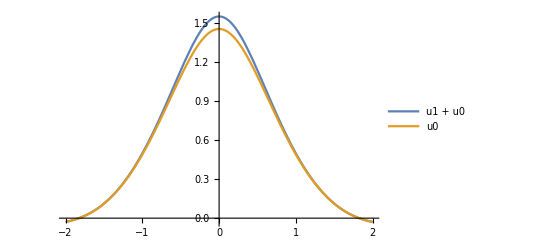

```mathematica
Plot[
{
u0[x] + u[1][x] /. %30 /. {A -> 0.43834, B -> 1.0170,σ->6^1/4},
u0[x] /. {A -> 0.43834, B -> 1.0170,σ->6^1/4}
}, 
{x, -2,2}, PlotLegends->{"u1 + u0", "u0"}]
```

### Check the answer

First check the simplification

```mathematica
Collect[(LDE[u[1]] + NDE[x |-> A CC[x] + B CC[x]]) /. Simplification, Sech[x σ]] /. answer /. {Sech[x σ]->sech} //Simplify
```

3/640 (A+B)^3 sech^5 (-64+43 sech^2) Γ

This holds

## u2

Try and see if we could use the u2 substitution instead

```mathematica
Collect[(LDE[u[1]] + NDE[x |-> A CC[x] + B CC[x]]) /. Simplification, Sech[x σ]] /. {A -> 1, B -> -1, Γ -> 24}
```

(64 σ^4 c[0]-96 σ^4 c[1]-192 σ^4 c[2]+352 σ^4 c[3]) Sech[x σ]^3+(-96 σ^4 c[0]+8 σ^4 c[1]-96 σ^4 c[2]-696 σ^4 c[3]) Sech[x σ]^5+(33 σ^4 c[0]+9 σ^4 c[1]+9 σ^4 c[2]+33 σ^4 c[3]) Sech[x σ]^7

```mathematica
Collect[(LDE[u[2]] + NDE[x |-> A CC[x] + B CC[x]]) /. Simplification, Sech[x σ]] /. {A -> 1, B -> -1, Γ -> 24}
```

(224 σ^4 c[0]-96 σ^4 c[1]-544 σ^4 c[2]-544 σ^4 c[3]+864 σ^4 c[4]+5024 σ^4 c[5]) Sech[x σ]^5+(-280 σ^4 c[0]-48 σ^4 c[1]+72 σ^4 c[2]-208 σ^4 c[3]-1176 σ^4 c[4]-3120 σ^4 c[5]) Sech[x σ]^7+(85 σ^4 c[0]+37 σ^4 c[1]+13 σ^4 c[2]+13 σ^4 c[3]+37 σ^4 c[4]+85 σ^4 c[5]) Sech[x σ]^9

```mathematica
Solve[24+72 B+72 B^2+24 B^3==0, B]
```

{{B→-1},{B→-1},{B→-1}}

## u0

See if the method above works on u0 (just to check that it is valid)

```mathematica
Collect[LDE[x |-> A CC[x] + B CC[x]], {Sech[x σ]}] //. {Tanh[_] -> sech / csch, Coth[_] -> csch / sech, Sech[_] -> sech,  Csch[_] -> csch}
```

sech^5 (5 A σ^4 Cos[x σ]+5 B σ^4 Cos[x σ])+sech^3 (6 A σ^4 Cos[x σ]+6 B σ^4 Cos[x σ]-(18 A sech^2 σ^4 Cos[x σ])/csch^2-(18 B sech^2 σ^4 Cos[x σ])/csch^2-(20 A sech σ^4 Sin[x σ])/csch-(20 B sech σ^4 Sin[x σ])/csch)+sech (5 A σ^4 Cos[x σ]+5 B σ^4 Cos[x σ]-(6 A sech^2 σ^4 Cos[x σ])/csch^2-(6 B sech^2 σ^4 Cos[x σ])/csch^2+(A sech^4 σ^4 Cos[x σ])/csch^4+(B sech^4 σ^4 Cos[x σ])/csch^4-(4 A sech σ^4 Sin[x σ])/csch-(4 B sech σ^4 Sin[x σ])/csch+(4 A sech^3 σ^4 Sin[x σ])/csch^3+(4 B sech^3 σ^4 Sin[x σ])/csch^3)

```mathematica
MatrixForm/@(eqns = CoefficientList[CoefficientList[%17 sech^4 csch^4, sech],csch] //. {Γ -> 24, σ -> 6^(1/4)} // N )
```

{{},{},{},{},{},(0.
0.
0.
0.
30. A Cos[1.56508 x]+30. B Cos[1.56508 x]),(0.
0.
0.
-24. A Sin[1.56508 x]-24. B Sin[1.56508 x]),(0.
0.
-36. A Cos[1.56508 x]-36. B Cos[1.56508 x]
0.
36. A Cos[1.56508 x]+36. B Cos[1.56508 x]),(0.
24. A Sin[1.56508 x]+24. B Sin[1.56508 x]
0.
-120. A Sin[1.56508 x]-120. B Sin[1.56508 x]),(6. A Cos[1.56508 x]+6. B Cos[1.56508 x]
0.
-108. A Cos[1.56508 x]-108. B Cos[1.56508 x]
0.
30. A Cos[1.56508 x]+30. B Cos[1.56508 x])}

All the relevant terms for scaling 1/cosh, 1/sinh are identically 0, regardless of A and B, and therefore this expression holds to the first order (as expected).